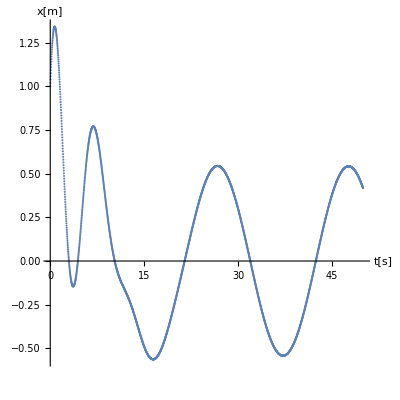

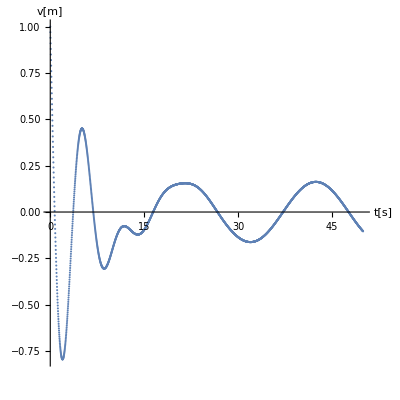

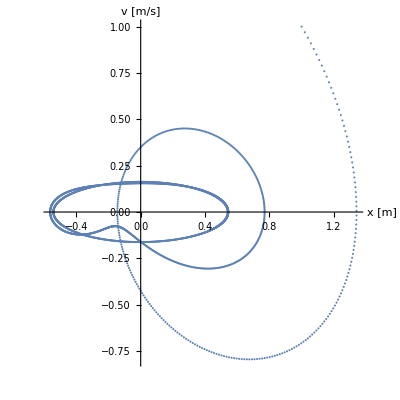

```mathematica
data=Import["/home/pedro/g0p2c0_out.txt", "Table"];
TableForm[data];

dataxt=data[[All,{1,2}]];
TableForm[dataxt];

datavt=data[[All,{1,3}]];
TableForm[datavt];

datavx=data[[All,{2,3}]];
TableForm[datavx];

Print[ListPlot[dataxt, AxesLabel->{"t[s]","x[m]"}, PlotRange-> {All,All},AspectRatio->1]];Print[ListPlot[datavt, AxesLabel->{"t[s]","v[m]"}, PlotRange-> {All,All},AspectRatio->1]];
Print[ListPlot[datavx, AxesLabel->{"x [m]","v [m/s]"}, PlotRange-> {All,All},AspectRatio->1]];
```